```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
sigmaSB=5.67*10^(-5); 
a=4*sigmaSB/c;   (*blackbody constant*)
Mu=0.62;     
gamma=5/3;
```

```mathematica
Polinomi=Table[q^i,{i,0,6}];
```

```mathematica
(*My data are in the form (log T, log R, opacity) = (kRList[[n,1]], kRList[[1,m]],kRList[[n,m]]),  n > 1, m > 1. Values determined by means of the OPAL code based on the solar composition detailed by N.Grevesse and A.Noels (1993) in Origin and Evolution of the Elements,eds.M.Pratzo, E.Vangioni-Flam and M.Casse (Cambridge:Cambridge Univ.Press). This is TABLE # 73 $G&N'93 Solar$ X=0.7000 Y=0.2800 Z=0.0200. Available from http://opalopacity.llnl.gov/existing.html#type1GN *)

kRList=Import["kR74GN93Solar.txt","Table"];

kRData=Flatten[Table[{{kRList[[n,1]],kRList[[1,m]]},10^(kRList[[n,m]])},{n,2,Dimensions[kRList][[1]]},{m,2,Dimensions[kRList][[2]]}],1];
kRS:=Interpolation[kRData];
kR[rho2_,T2_]:=kRS[Log10[T2],Log10[rho2/(T2/(10^6))^3]];
```

```mathematica
(*for fixed Rho, we expand kR = a0 + a1 T + a2 T^2 + a3 T^3 + a4 T^4. Then we fit a0, a1, a2, a3, a4 as polynomials in rho.*)

Tmin=1.79*10^6;
Tmax=3.89*10^6;
rhomin=0.13;
rhomax=0.8;

kTemporaryTable=Table[{rho,Table[{T,kR[rho,T]},{T,Tmin,Tmax,0.1*10^6}]},{rho,rhomin,rhomax,0.01}];

RhoANTable=Table[{kTemporaryTable[[i]][[1]],LinearModelFit[kTemporaryTable[[i]][[2]],Polinomi,q]["BestFitParameters"]},{i,1,Dimensions[kTemporaryTable][[1]]}];

A0Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[1]]},{i,1,Dimensions[RhoANTable][[1]]}];
A1Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[2]]},{i,1,Dimensions[RhoANTable][[1]]}];
A2Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[3]]},{i,1,Dimensions[RhoANTable][[1]]}];
A3Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[4]]},{i,1,Dimensions[RhoANTable][[1]]}];
A4Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[5]]},{i,1,Dimensions[RhoANTable][[1]]}];
A5Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[6]]},{i,1,Dimensions[RhoANTable][[1]]}];
A6Table=Table[{RhoANTable[[i]][[1]],RhoANTable[[i]][[2]][[7]]},{i,1,Dimensions[RhoANTable][[1]]}];

A0=Fit[A0Table,Polinomi,q];
A0fit[rho_]=A0/.{q->rho};
A1=Fit[A1Table,Polinomi,q];
A1fit[rho_]=A1/.{q->rho};
A2=Fit[A2Table,Polinomi,q];
A2fit[rho_]=A2/.{q->rho};
A3=Fit[A3Table,Polinomi,q];
A3fit[rho_]=A3/.{q->rho};
A4=Fit[A4Table,Polinomi,q];
A4fit[rho_]=A4/.{q->rho};
A5=Fit[A5Table,Polinomi,q];
A5fit[rho_]=A5/.{q->rho};
A6=Fit[A6Table,Polinomi,q];
A6fit[rho_]=A6/.{q->rho};

kRFit[rho_,T_]=A0fit[rho]+A1fit[rho]T+A2fit[rho]T^2+A3fit[rho]T^3+A4fit[rho]T^4+A5fit[rho]T^5+A6fit[rho]T^6;

kRFitDerivRho[rho_,T_]=D[kRFit[rho,T],rho];
kRFitDerivTemp[rho_,T_]=D[kRFit[rho,T],T];

Show[Plot[kR[rho,2*10^6],{rho,0.13,0.8}],Plot[kRFit[rho,2*10^6],{rho,rhomin,rhomax},PlotStyle->Red],Frame->True,FrameLabel->{"rho (g/cm^3)","k (cm^2/g)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
Show[Plot[kR[0.2,T],{T,1.8*10^6,4*10^6}],Plot[kRFit[0.2,T],{T,Tmin,Tmax},PlotStyle->Red],Frame->True,FrameLabel->{"T (K)","k (cm^2/g)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
SolarModel0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\SolarModelBS2005-AGS,OP","Table"];

SolarModel=Drop[SolarModel0,1];
SolarModel=Drop[SolarModel,-3];
```

```mathematica
RadiusMass=Table[{ Rsun*SolarModel[[All,2]][[i]],Msun*SolarModel[[All,1]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusTemp=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,3]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusDens=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,4]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusPress=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,5]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusLumin=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
```

```mathematica
RadiusFlux=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]/(4*Pi*(RadiusTemp[[i]][[1]])^2)},{i,1,Dimensions[SolarModel][[1]]}];

RadiusGrav=Table[{RadiusMass[[i]][[1]],G*RadiusMass[[i]][[2]]/(RadiusMass[[i]][[1]])^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];
```

```mathematica
RDown=Rsun*0.55;
RUp=Rsun*0.8;
Rstart=rStart*Rsun;
Rend=Rsun*0.73;
rEnd=Rend/Rsun;
rEndPlot=0.725;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
```

```mathematica
GravFit0=Fit[RadiusGravReduced,Polinomi,q];
GravFit[x_]=GravFit0/.{q->x};
Show[Plot[Grav[r],{r,RDown,RUp}],ListPlot[RadiusGravReduced],Plot[GravFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","g (cm/s^2)","Gravity"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
cConst1=3*Lsun/(16*Pi*a*c);
```

```mathematica
P2[r_]:=-0.5*r^2*X0[r];
P4[r_]:=-0.25*r^2*X2[r];
Rho2[r_]:=(r/GravFit[r])*(X2[r]-X0[r])+(1/(2*GravFit[r]))*D[r^2*X0[r],r]
Rho4[r_]:=-(r/GravFit[r])*X2[r]+(1/(4*GravFit[r]))*D[r^2*X2[r],r]
```

```mathematica
Equation2:=(5cConst1/r^2)D[Rho2[r]/RhoFit[r],r]-(4cConst1/r^2)*D[P2[r]/PressFit[r],r]+(1/r^2)*
D[((r^2*TempFit[r]^4)/(RhoFit[r]*kRFit[RhoFit[r],TempFit[r]]))*(D[P2[r]/PressFit[r],r]-D[Rho2[r]/RhoFit[r],r]),r]+
(1/r^2)*D[(cConst1/kRFit[RhoFit[r],TempFit[r]])*(Rho2[r]*kRFitDerivRho[RhoFit[r],TempFit[r]]+TempFit[r]*kRFitDerivTemp[RhoFit[r],TempFit[r]]*(P2[r]/PressFit[r]-Rho2[r]/RhoFit[r])),r]+(TempFit[r]^4/(r^2*RhoFit[r]*kRFit[RhoFit[r],TempFit[r]]))*(4*3*(P4[r]/PressFit[r]-Rho4[r]/RhoFit[r])-3*2*(P2[r]/PressFit[r]-Rho2[r]/RhoFit[r]))

Equation4:=(5cConst1/r^2)D[Rho4[r]/RhoFit[r],r]-(4cConst1/r^2)*D[P4[r]/PressFit[r],r]+(1/r^2)*
D[((r^2*TempFit[r]^4)/(RhoFit[r]*kRFit[RhoFit[r],TempFit[r]]))*(D[P4[r]/PressFit[r],r]-D[Rho4[r]/RhoFit[r],r]),r]+
(1/r^2)*D[(cConst1/kRFit[RhoFit[r],TempFit[r]])*(Rho4[r]*kRFitDerivRho[RhoFit[r],TempFit[r]]+TempFit[r]*kRFitDerivTemp[RhoFit[r],TempFit[r]]*(P4[r]/PressFit[r]-Rho4[r]/RhoFit[r])),r]+(TempFit[r]^4/(r^2*RhoFit[r]*kRFit[RhoFit[r],TempFit[r]]))*(-5*4*(P4[r]/PressFit[r]-Rho4[r]/RhoFit[r]))
```

```mathematica
c10=1.00523*1;
c20=-3.81029*1.11;
c30=-0.14306647*1.08;
c40=1.00098*0.86;
c50=-50.36242*1.06;
c60=2.4291*1.22;

ChiSqValue:=Sum[(OmegaSq0Fit[r]-Om0SqSol[r*Rsun])^2/OmegaSq0Fit[r]^2+(OmegaSq2Fit[r]-Om2SqSol[r*Rsun])^2/OmegaSq2Fit[r]^2,{r,rStart,rEnd,0.01}]
```

```mathematica
SolutionProcedure:={
c1=c10*k1;
c2=c20*k2;
c3=c30*k3;
c4=c40*k4;
c5=c50*k5;
c6=c60*k6;

OmSq0start=c1*OmegaSq0Fit[rStart];
OmSq0startDeriv=c2*OmegaSq0Fit'[rStart]/Rsun;
OmSq0startDeriv2=c3*OmegaSq0Fit''[rStart]/Rsun^2;
OmSq2start=c4*OmegaSq2Fit[rStart];
OmSq2startDeriv=c5*OmegaSq2Fit'[rStart]/Rsun;
OmSq2startDeriv2=c6*OmegaSq2Fit''[rStart]/Rsun^2;

X0start=RhoFit[Rstart]*OmSq0start;
X0startDeriv=RhoFit'[Rstart]*OmSq0start+RhoFit[Rstart]*OmSq0startDeriv;
X0startDeriv2=RhoFit''[Rstart]*OmSq0start+2*RhoFit'[Rstart]*OmSq0startDeriv+RhoFit[Rstart]*OmSq0startDeriv2;
X2start=RhoFit[Rstart]*OmSq2start;
X2startDeriv=RhoFit'[Rstart]*OmSq2start+RhoFit[Rstart]*OmSq2startDeriv;
X2startDeriv2=RhoFit''[Rstart]*OmSq2start+2*RhoFit'[Rstart]*OmSq2startDeriv+RhoFit[Rstart]*OmSq2startDeriv2;
BoundaryConditions={X0[Rstart]==X0start,X0'[Rstart]==X0startDeriv,
X0''[Rstart]==X0startDeriv2,X2[Rstart]==X2start,X2'[Rstart]==X2startDeriv,
X2''[Rstart]==X2startDeriv2};
Equations:=Flatten[Append[{Equation2==0,Equation4==0},BoundaryConditions]];
Xsol0=NDSolve[Equations,{X0,X2},{r,Rstart,Rend}];

X0sol[x_]=((X0[r]/.Xsol0)/.{r->x})[[1]];
X2sol[x_]=((X2[r]/.Xsol0)/.{r->x})[[1]];
X0solTable=Table[{r,X0sol[r]},{r,Rstart,Rend,0.01Rsun}];
X0solFit0=Fit[X0solTable,Polinomi,q];
X0solFit[x_]=X0solFit0/.{q->x};
Show[ListPlot[X0solTable],Plot[X0solFit[r],{r,Rstart,Rend}]];

X2solTable=Table[{r,X2sol[r]},{r,Rstart,Rend,0.01Rsun}];
X2solFit0=Fit[X2solTable,Polinomi,q];
X2solFit[x_]=X2solFit0/.{q->x};
Show[ListPlot[X2solTable],Plot[X2solFit[r],{r,Rstart,Rend}]];
Om0SqSolPure[r_]=(X0sol[r]/RhoFit[r]);
Om2SqSolPure[r_]=(X2sol[r]/RhoFit[r]);
Om0SqSol[r_]=(X0solFit[r]/RhoFit[r]);
Om2SqSol[r_]=(X2solFit[r]/RhoFit[r]);

OmegaSq0SolPure[x_]=Om0SqSolPure[x*Rsun];
OmegaSq2SolPure[x_]=Om2SqSolPure[x*Rsun];
OmegaSq0Sol[x_]=Om0SqSol[x*Rsun];
OmegaSq2Sol[x_]=Om2SqSol[x*Rsun];};
```

```mathematica
Table[SolutionProcedure;
{{k1,k2,k3,k4,k5,k6},ChiSqValue},{k1,1.,1.},{k2,1,1},{k3,1,1},{k4,1,1},{k5,1,1},{k6,1,1}];
```

```mathematica
Om0SqSolBest[q_]=Om0SqSol[q];
Om2SqSolBest[q_]=Om2SqSol[q];
```

```mathematica
Show[Plot[OmegaSq0Fit[r],{r,Rstart/Rsun,rEndPlot},PlotStyle->Black],Plot[Om0SqSol[r*Rsun],{r,Rstart/Rsun,rEndPlot},PlotStyle->Directive[Black, Dashed],PlotRange->{{rStart,rEndPlot},{5.5*10^-12,9*10^-12}}],PlotRange->{{rStart,rEndPlot},{5.5*10^-12,9*10^-12}},Frame->True,FrameLabel->{"r/R_⊙","Ω_0^2(s^-2)"},BaseStyle->{FontWeight->"Bold",FontSize->19},Axes->None];
Show[Plot[OmegaSq2Fit[r],{r,Rstart/Rsun,rEndPlot},PlotStyle->Black],Plot[Om2SqSol[r*Rsun],{r,Rstart/Rsun,rEndPlot},PlotStyle->Directive[Black,Dashed]],PlotRange->{{rStart,rEndPlot},{-3.5*10^-12,10^-12}},Frame->True,FrameLabel->{"r/R_⊙","Ω_2^2(s^-2)"},BaseStyle->{FontWeight->"Bold",FontSize->19},Axes->None,GridLines->{{},{0}}];
```

```mathematica
k1=1;
k2=0.5;
k3=0.5;
k4=1;
k5=0.5;
k6=0.5;

SolutionProcedure;

Om0SqSolHalf[q_]=Om0SqSol[q];
Om2SqSolHalf[q_]=Om2SqSol[q];
```

```mathematica
k1=1;
k2=2;
k3=2;
k4=1;
k5=2;
k6=2;

SolutionProcedure;

Om0SqSolDouble[q_]=Om0SqSol[q];
Om2SqSolDouble[q_]=Om2SqSol[q];
```

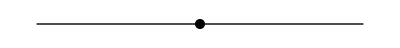
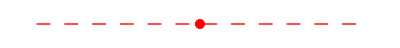
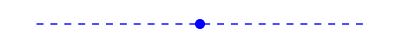
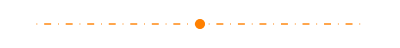
-Graphics- | GONG Data
-Graphics- | Radiative Equilibrium (best fit)
-Graphics- | Radiative Equilibrium (model a)
-Graphics- | Radiative Equilibrium (model b)

```mathematica
CaptionGeneral[{{"GONG Data",Black,Thick},{"Radiative Equilibrium (best fit)",Red, Dashing[{0.025,0.025}]},{"Radiative Equilibrium (model a)",Blue,Dashed},{"Radiative Equilibrium (model b)",Orange,DotDashed}}]
```

```mathematica
Show[Plot[OmegaSq0Fit[r],{r,Rstart/Rsun,rEndPlot},PlotStyle->Directive[Black,Thick]],ListPlot[Table[{r,Om0SqSolHalf[r*Rsun]},{r,rStart,rEndPlot,0.003}],PlotStyle->Directive[Blue,PointSize[0.008]],PlotRange->{{rStart,rEndPlot},{7*10^-12,9*10^-12}}],Plot[Om0SqSolBest[r*Rsun],{r,Rstart/Rsun,rEndPlot},PlotStyle->Directive[Red,Thick, Dashing[{0.02,0.02}]],PlotRange->{{rStart,rEndPlot},{7*10^-12,9*10^-12}}],ListPlot[Table[{r,Om0SqSolDouble[r*Rsun]},{r,rStart,rEndPlot,0.003}],PlotMarkers->{"+",15},PlotStyle->Orange,PlotRange->{{rStart,rEndPlot},{7*10^-12,9*10^-12}}],PlotRange->{{rStart,rEndPlot},{7*10^-12,9*10^-12}},Frame->True,FrameLabel->{"r/R_⊙","Ω_0^2(s^-2)"},BaseStyle->{FontWeight->"Bold",FontSize->19},Axes->None,AspectRatio->1/1.8]


Show[Plot[OmegaSq2Fit[r],{r,Rstart/Rsun,rEndPlot},PlotStyle->Directive[Black,Thick]],ListPlot[Table[{r,Om2SqSolHalf[r*Rsun]},{r,rStart,rEndPlot,0.003}],PlotStyle->Directive[Blue,PointSize[0.008]],
PlotRange->{{rStart,rEndPlot},{-3.5*10^-12,2*10^-12}}],Plot[Om2SqSolBest[r*Rsun],{r,rStart,rEndPlot},PlotStyle->Directive[Red,Thick,Dashing[{0.02,0.02}]],PlotRange->{{rStart,rEndPlot},{-3.5*10^-12,2*10^-12}}],
ListPlot[Table[{r,Om2SqSolDouble[r*Rsun]},{r,Rstart/Rsun,rEndPlot,0.003}],PlotMarkers->{"+",15},PlotStyle->Orange,PlotRange->{{rStart,rEndPlot},{-3.5*10^-12,2*10^-12}}],PlotRange->{{rStart,rEndPlot},{-3.5*10^-12,2*10^-12}},Frame->True,FrameLabel->{"r/R_⊙","Ω_2^2(s^-2)"},BaseStyle->{FontWeight->"Bold",FontSize->19},Axes->None,GridLines->{{},{0}},AspectRatio->1/1.8]
```

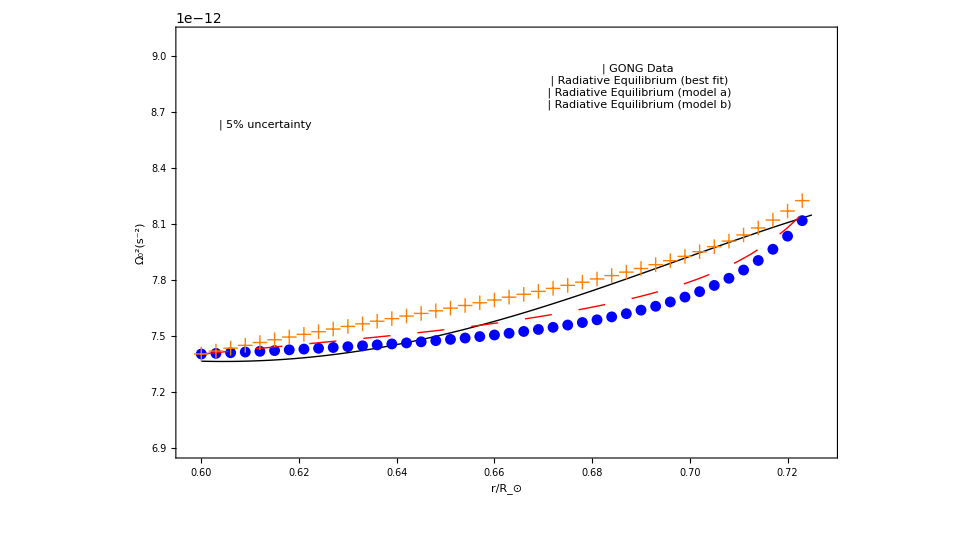

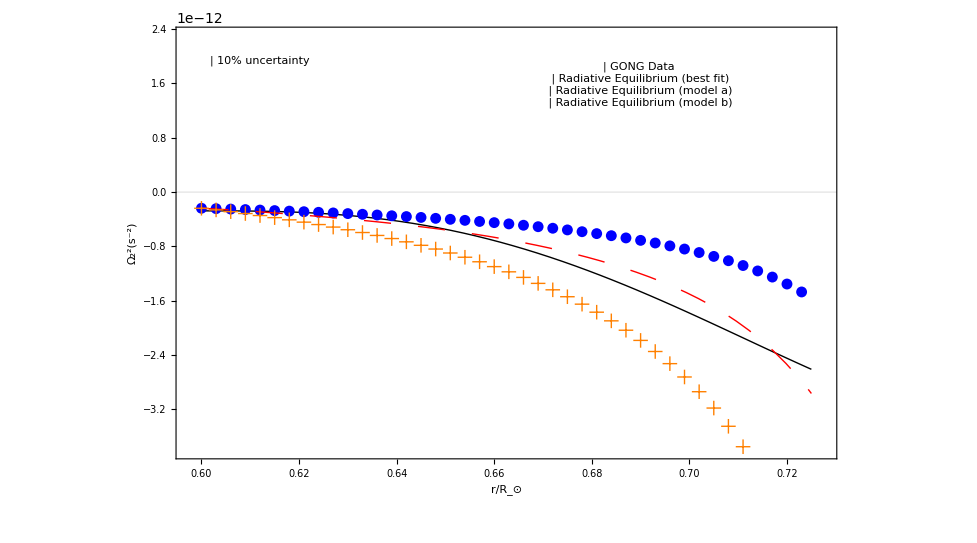

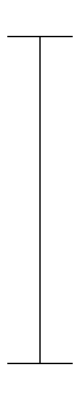
-Graphics- | 10% uncertainty

```mathematica
Framed[
Grid[
{{Graphics[{Line[{{0,0},{0.05,0}}],Line[{{0.025,0},{0.025,0.25}}],Line[{{0,0.25},{0.05,0.25}}]}],"10% uncertainty"}}
]
]
```

```mathematica
k1=1;
k2=1;
k3=1;
k4=1;
k5=1;
k6=1;

SolutionProcedure;
```

```mathematica
FigOmega0 = -Graphics-;
FigOmega2 = -Graphics-;
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Paper 1\\Final\\Code\\FigOmega0.png",FigOmega0,ImageResolution-> 150]
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Paper 1\\Final\\Code\\FigOmega2.png",FigOmega2,ImageResolution-> 150]*)
```

C:\Users\Pigkappa\Dropbox\fisica\PhD\Paper 1\Final\Code\FigOmega0.png

C:\Users\Pigkappa\Dropbox\fisica\PhD\Paper 1\Final\Code\FigOmega2.png